```mathematica
<<Local`QFTToolKit2`
tuItalics
```

Mon 29 Oct 2018 14:15:02

```mathematica
tuGraphicDefs
$=$coordSolidAngle={CG["Solid angle for sphere S^(n - 1)"],
{T[ω,"u",{1}]->Cos[T[θ,"d",{1}]],
{T[ω,"u",{i}]->Product[Sin[T[θ,"d",{j}]],{j,1,i-1}]Cos[T[θ,"d",{i}]],{i,1,n-1}},
T[ω,"u",{n}]->Product[Sin[T[θ,"d",{j}]],{j,1,n-2}]Sin[T[θ,"d",{n-1}]],
{{0≤T[θ,"d",{i}]<π,1≤i<n-1},
0≤T[θ,"d",{n-1}]<2π
}
}[CG["define direction cosines"]],
$coordSolidAngleDiff={xSum[T[ω,"u",{i}]^2,{i,1,n}]->1,
d[Subscript[Ω, n-1]]^2->xSum[d[T[ω,"u",{i}]]^2,{i,1,n}],
xSum[T[ω,"u",{i}]d[T[ω,"u",{i}]],{i,1,n}]->0
}[CG["$coordSolidAngleDiff"]]
}[CG["$coordSolidAngle"]];(ColumnForms[#1,5]&)[$]
```

Solid angle for sphere S^(n - 1)
ω_1^1→Cos[θ_1^1]
ω_i^i→Cos[θ_i^i] ∏_(j=1)^(-1+i) Sin[θ_j^j]
{i,1,-1+n}
ω_n^n→(∏_(j=1)^(-2+n) Sin[θ_j^j]) Sin[θ_(-1+n)^(-1+n)]
{0≤θ_i^i<π,1≤i<-1+n}
0≤θ_(-1+n)^(-1+n)<2 π[define direction cosines]
UnderBar[∑]_{i,1,n}[(ω_i^i)^2]→1
d[Ω_(-1+n)]^2→UnderBar[∑]_{i,1,n}[d[ω_i^i]^2]
UnderBar[∑]_{i,1,n}[d[ω_i^i] ω_i^i]→0[$coordSolidAngleDiff][$coordSolidAngle]

```mathematica
$metricSchwarzschild={
d[s]^2->-(1-2M G/r)d[t]^2+(1-2M G/r)^-1 d[r]^2+r^2(d[θ]^2+Sin[θ]^2 d[ϕ]^2)}[CG["$metricSchwarzschild"]]

$metricMinkowski={
tuRule[$metricSchwarzschild]/.M->0}[CG["$metricMinkowski"]]

$metricNullCoordinateMinkowski=$={
{$uv={u->(t-r),v->(t+r)}}[CG["$uv null coordinates"]],
$tr=tuRuleSolve[$uv,{t,r}],
tuRule[$metricMinkowski]/.$tr//tudExpand[d,{}]//Simplify
};(ColumnForms[#1,2]&)[$][CG["$metricNullCoordinateMinkowski"]]

$metricPenrose=$={
$coordPenrose={v->Tan[ṽ],u->Tan[ũ],{ṽ,ũ}∈Interval[{-π/2,π/2}]}[CG["$coordPenrose"]],
tuRuleSolve[tuRule[$coordPenrose],{ṽ,ũ}]//Refine[#,C[1]==0&&C[2]==0]&,
($metricNullCoordinateMinkowski//tuRuleSelect[d[s]^2]//First)/.tuRule[$coordPenrose]//tuOpIndependentVar[tudExpand,op$[d][#]]&//Simplify
};(ColumnForms[#1,2]&)[$][CG["$metricPenrose"]]


$metricSchwarzschildKruskalSzekeres=$={$coordSchwarzschildKruskalSzekeres={{T->√Abs[r/(2M G)-1] Exp[r/(4M G)](Sinh[t/(4M G)]HeavisideTheta[r-2M G]+Cosh[t/(4M G)]HeavisideTheta[2M G-r]),X->√Abs[r/(2M G)-1] Exp[r/(4M G)](Cosh[t/(4M G)]HeavisideTheta[r-2M G]+Sinh[t/(4M G)]HeavisideTheta[2M G-r])}}[CG["$coordSchwarzschildKruskalSzekeres"]],
$00=$=$coordSchwarzschildKruskalSzekeres//tuRule;
$0=$s=$[[1;;2]];
$=T^2-X^2;
$=$->($/.$s)//Simplify;{$}[CG["Null geodesic at r→2MG"]],

$s2M=(r>2M G);
$=Inactive[Refine][$,$s2M],
$=$//Activate;
$sr=tuRuleSolve[$,{r}]//First,
$=Refine[$00,$s2M],
$=tuRuleSolve[$[[1]],{t}]//Refine[#,C[1]==0]&;
$=$/.$sr//FullSimplify;
{$sr,$//Last},
$=tuRule[$coordSchwarzschildKruskalSzekeres][[1;;2]]//Refine[#,$s2M]&;
$s=(d/@#)&/@$/.Abs[a_]->a//tudExpand[d,{M,G}];
$=$0=-d[T]^2+d[X]^2;
$=$0->($/.$s//Simplify);
$metricKrukalSzekeres=$={$,Exp[-r/(2M G)]32 (M G)^3#/r&/@$//Collect[#,d[_],Simplify]&//Simplify};$[CG["$metricKrukalSzekeres"]],

$metricKrukalSzekeresNull=$={$s={T->(U-V)/2,X->(U+V)/2},
$metricKrukalSzekeres/.$s//tudExpand[d]//Simplify};$[CG["$metricKrukalSzekeresNull"]]

};(ColumnForms[#1,4]&)[$][CG["$metricSchwarzschildKruskalSzekeres"]]


$einsteinEqn={T[R,"dd"][μ,ν]-T[g,"dd"][μ,ν]T[R,{},{}]/2+Λ T[g,"dd"][μ,ν]->8π T[T,"dd"][μ,ν]}[CG["$einsteinEqn"]]
```

{d[s]^2→d[r]^2/(1-(2 G M)/r)+(-1+(2 G M)/r) d[t]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}[$metricSchwarzschild]

{{d[s]^2→d[r]^2-d[t]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}}[$metricMinkowski]

{{u→-r+t,v→r+t}}[$uv null coordinates]
t→(u+v)/2
r→1/2 (-u+v)
d[s]^2→-d[u] d[v]+1/4 (u-v)^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)[$metricNullCoordinateMinkowski]

{v→Tan[ṽ],u→Tan[ũ],{ṽ,ũ}∈Interval[{-π/2,π/2}]}[$coordPenrose]
ṽ→ArcTan[v]
ũ→ArcTan[u]
d[s]^2→-d[ũ] d[ṽ] Sec[ũ]^2 Sec[ṽ]^2+1/4 (d[θ]^2+d[ϕ]^2 Sin[θ]^2) (Tan[ũ]-Tan[ṽ])^2[$metricPenrose]

T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])[$coordSchwarzschildKruskalSzekeres]
T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2)[Null geodesic at r→2MG]
Refine[T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2),r>2 G M]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Sinh[t/(4 G M)]
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Cosh[t/(4 G M)]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
t→4 G M ArcSinh[(ⅇ^(1/2 (-1-ProductLog[((T-X) (T+X))/ⅇ])) T)/(√Abs[ProductLog[((T-X) (T+X))/ⅇ]])]
-d[T]^2+d[X]^2→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r))
-(32 ⅇ^(-r/(2 G M)) G^3 M^3 (d[T]^2-d[X]^2))/r→-(r d[r]^2)/(2 G M-r)+(-1+(2 G M)/r) d[t]^2[$metricKrukalSzekeres]
T→(U-V)/2
X→(U+V)/2
d[U] d[V]→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r))
(32 ⅇ^(-r/(2 G M)) G^3 M^3 d[U] d[V])/r→-(r d[r]^2)/(2 G M-r)+((2 G M-r) d[t]^2)/r[$metricKrukalSzekeresNull][$metricSchwarzschildKruskalSzekeres]

{Λ g_μν^μν-1/2 g_μν^μν R_^+R_μν^μν→8 π T_μν^μν}[$einsteinEqn]

```mathematica
$metricEddingtonFinkelstein=$={$coordEddingtonFinkelstein={{v->t+SuperStar[r][CG["tortoise coordinate"]]}[CG["ingoing null ray"]],
{u->t-SuperStar[r][CG["tortoise coordinate"]]}[CG["outgoing null ray"]]},
$=$coordTortoise={$=SuperStar[r][CG["tortoise coordinate"]]->r+2 G M Log[Abs[r/(2 G M)-1]],
$sr=tuOpIndependentVar[tuRuleSolve,op$[$,r]]//tuRule//First,
$sr1=$sr//tuRuleSolveF[ProductLog[_]]//FullSimplify//First,
$sr2=$sr//tuRuleSolveF[SuperStar[r]]//First,
{$s=$coordEddingtonFinkelstein//tuRuleSelect[v]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinIn=$dsv=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinIn"]]//Framed
},
{$s=$coordEddingtonFinkelstein//tuRuleSelect[u]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinOut=$dsu=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinOut"]]//Framed
}
}
};
{(ColumnForms[#1,2]&)[$]}[CG["$metricEddingtonFinkelstein"]]
```

{{v→t+r^*[tortoise coordinate]}[ingoing null ray]
{u→t-r^*[tortoise coordinate]}[outgoing null ray]
r^*[tortoise coordinate]→r+2 G M Log[Abs[-1+r/(2 G M)]]
r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])
ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M)
r^*→2 (G M+G M Log[(ⅇ^(-1+r/(2 G M)) (-2 G M+r))/(2 G M)])
{r^*→-t+v,r→2 (G M+G M ProductLog[ⅇ^(-1+(-t+v)/(2 G M))]),{d[s]^2→2 d[r] d[v]+(-1+(2 G M)/r) d[v]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}[$metricEddingtonFinkelsteinIn]}
{r^*→t-u,r→2 (G M+G M ProductLog[ⅇ^(-1+(t-u)/(2 G M))]),{d[s]^2→-2 d[r] d[u]+(-1+(2 G M)/r) d[u]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}[$metricEddingtonFinkelsteinOut]}}[$metricEddingtonFinkelstein]

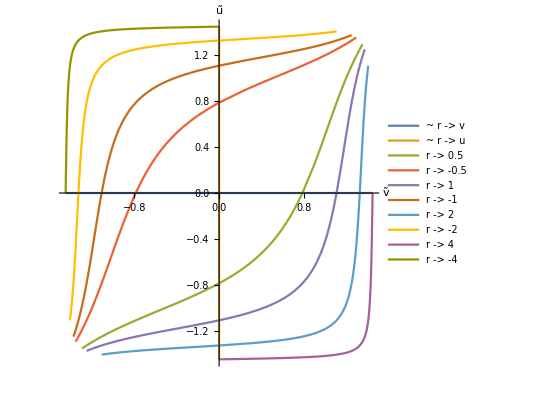
Penrose diagram of Minkowski space(clockwise rotated 45^o from traditional plot)
→ {u,v}→{-r+t,r+t}
→ {ṽ,ũ}→{ArcTan[v],ArcTan[u]}
→ {ṽ,ũ}→{ArcTan[r+t],-ArcTan[r-t]}
-Graphics-

```mathematica
PR["Penrose diagram of Minkowski space(clockwise rotated 45^o from traditional plot)",
$metricNullCoordinateMinkowski;
$=$0={u,v};
Yield,$=$0->($/.tuRule[$metricNullCoordinateMinkowski]),
$metricPenrose;
$=$1={ṽ,ũ};
Yield,$=$1->($1/.tuRule[$metricPenrose]),
$[[2]]=$[[2]]/.tuRule[$metricNullCoordinateMinkowski];
Yield,$2=$,
$[[2]]=$[[2]]/.t->0//Limit[#,r->-∞]&;

$=$2[[2]];
$t=Table[{$/.r->ii,$/.r->-ii},{ii,{t,.5,1,2,4}}]//Flatten[#,1]&;
$legend=Table[{r->ii,r->-ii},{ii,{t,.5,1,2,4}}]/.{ -t->ũ,t->ṽ}//Flatten;
$legend=ToString/@$legend;
NL,
ParametricPlot[$t,{t,-4,4},AxesLabel->$1,PlotLegends->$legend]
];
```

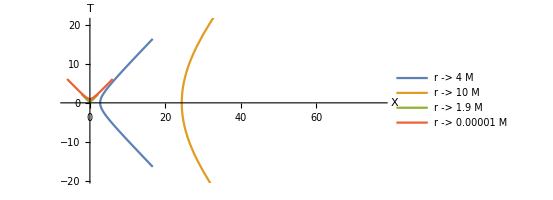
Plot of Schwarzschild solution: $metricSchwarzschildKruskalSzekeres
$coordSchwarzschildKruskalSzekeres T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])
For {M→1,G→1} and r: {4 M,10 M,1.9 M,0.00001 M}
→ {X,T}-Graphics-

```mathematica
PR["Plot of Schwarzschild solution: $metricSchwarzschildKruskalSzekeres",
NL,"$coordSchwarzschildKruskalSzekeres ",$0=tuRule[$coordSchwarzschildKruskalSzekeres];(ColumnForms[#1,2]&)[$0],
$sM={M->1,G->1};
NL,"For ",$sM," and r: ",$rs=Table[r,{r,M{4,10,1.9,.00001}}],
Yield,$label=$00={X,T},
$t=Table[$label/.($0),{r,$rs}]/.$sM;
$legend=ToString/@Thread[r->$rs];
ParametricPlot[$t,{t,-10,10},AxesLabel->$label,PlotLegends->$legend]
]
(*ParametricPlot[$t,{t,-10,10},AxesLabel->$label,PlotLegends->$legend]*)
```

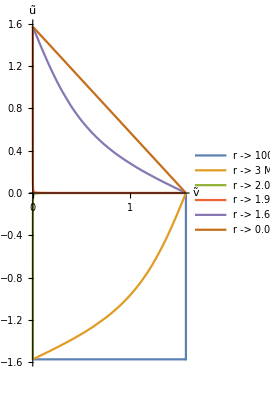
Penrose diagram for $metricSchwarzschildKruskalSzekeres
$coordSchwarzschildKruskalSzekeres T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)]){u→T-X,v→T+X} and {ṽ→ArcTan[v],ũ→ArcTan[u]}
For {M→1,G→1}
This is Penrose-Carter diagram of the Schwarzschild solution clockwise rotated by 45^o. The ṽ<0 region are not shown. The lines -Graphics-
{r -> 100 M, close to r→∞, ℐ^±,𝒾^*}
{r -> 2.0001 M, close to r→2M, ũ|ṽ→0}
{r -> 0.00001 M, close to r→0, singularity}$plotPenroseKruskalSzekeres

```mathematica
PR["Penrose diagram for $metricSchwarzschildKruskalSzekeres",
NL,"$coordSchwarzschildKruskalSzekeres ",$0=tuRule[$coordSchwarzschildKruskalSzekeres];(ColumnForms[#1,2]&)[$0],
$label={ṽ,ũ};
$suv={u->T-X,v->T+X},and,
$=tuRuleSelect[$label][$metricPenrose],
$=MapAt[#/.$suv&,#,2]&/@$;
$1=$/.$0;
NL,"For ",$sM,
$rs=Table[r,{r,M{100,3,2.0001,1.9999,1.6,.00001}}];
$t=Table[$label/.($1),{r,$rs}]/.$sM;
$legend=ToString/@Thread[r->$rs];
$plotPenroseKruskalSzekeres=ParametricPlot[$t,{t,-100,100},AxesLabel->$label,PlotLegends->$legend];
NL,"This is Penrose-Carter diagram of the Schwarzschild solution clockwise rotated by 45^o. The ṽ<0 region are not shown. The lines ",
$={{$legend[[1]]," close to r→∞, ℐ^±,𝒾^*"},
{$legend[[3]]," close to r→2M, ũ|ṽ→0"},
{$legend[[-1]]," close to r→0, singularity"}
};(ColumnForms[#1,2]&)[$];
$=$plotPenroseKruskalSzekeres={$plotPenroseKruskalSzekeres,$};(ColumnForms[#1,2]&)[$],CG["$plotPenroseKruskalSzekeres"]
];
```

Extended conformal Schwarzschild spacetime{T[-π/2,π/2],X[-π/2,π/2]} $plotPenroseKruskalSzekeres diagram centered on M Fig.12.2

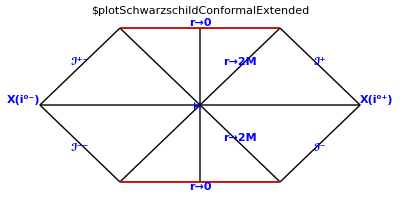

```mathematica
PR["Extended conformal Schwarzschild spacetime{T[-π/2,π/2],X[-π/2,π/2]} $plotPenroseKruskalSzekeres diagram centered on M Fig.12.2"];

$plotSchwarzschildConformalExtended:={$vx={Range[-3,3],Range[-3,3]}//Tuples;
$offset=.3;
tuGraphicDefs;
Graphics[MapIndexed[Text[#2,#1]&,$vx]];

$line={{mid[34,40],$vx[[46]]},
{mid[30,38],$vx[[46]]},

{$vx[[25]],mid[26,27]},
{mid[23,24],$vx[[25]]},

{mid[10,16],$vx[[25]]},
{mid[12,20],mid[34,40]},

{mid[10,16],mid[30,38]},
{$vx[[25]],mid[30,38]},

{mid[12,20],$vx[[25]]},
{$vx[[25]],mid[34,40]},

{$vx[[4]],$vx[[25]]},
{$vx[[25]],$vx[[46]]},
{$vx[[4]],mid[12,20]},
{$vx[[4]],mid[10,16]}

};

Graphics[{Thin,Black,Map[Line[#]&,$line],
Thick,Red,Line[$line[[6]]],Line[$line[[7]]],
Blue,(*
MapIndexed[Text[#2,(#1[[1]]+#1[[2]])/2]&,$line],*)

Text[Style[T,Bold,Medium],$vx[[25]],{0,-$offset},{0,1}],
Text[Style[X[ii^("0+")],Bold,Medium],$vx[[46]],{-4 $offset,-2 $offset}],
Text[Style[X[ii^("0-")],Bold,Medium],$vx[[4]],{4 $offset,-2 $offset}],

Text[Style["ℐ^-",Bold,Medium],midline[2],{ $offset,2 $offset},{1,1}],
Text[Style["ℐ^(--)",Bold,Medium],midline[14],{ $offset,2 $offset},{1,-1}],

Text[Style["ℐ^+",Bold,Medium],midline[1],{$offset,-3 $offset},{1,-1}],
Text[Style["ℐ^(+-)",Bold,Medium],midline[13],{$offset,-3 $offset},{1,1}],
Text[Style["r→0",Bold,Medium],midline[6],{$offset,-3 $offset},{1,0}],
Text[Style["r→0",Bold,Medium],midline[7],{$offset,3 $offset},{1,0}],
Text[Style["r→2M",Bold,Medium],midline[10],{$offset,-3 $offset},{1,1}],
Text[Style["r→2M",Bold,Medium],midline[8],{$offset,-3 $offset},{1,-1}]
},PlotLabel->"$plotSchwarzschildConformalExtended"
]
}
$plotSchwarzschildConformalExtended
```

```mathematica
tuSaveAllVariables[]
```